```mathematica
(*All units in mm*)
newstep[n_]:=newstep[n-1](ideal[n]/act[n])
newstepwex[n_]:=newstepwex[n-1](idealwex[n]/actwex[n])
error[n_]:=(ideal[n]/act[n])
```

```mathematica
defaultstep={79.6814,79.6364,3989.4};
defaultstepwex={80.03,80.15,398.02,670};

newstep[0]=defaultstep;
newstepwex[0]=defaultstepwex;
```

```mathematica
(* Ideal is value expected,  act(ual) value is what is measured.
Generates a correction. 

Please keep defaultstep up to date!
*)
```

```mathematica
(* New cal as of 2/25/2018 *)
```

```mathematica
newstepwex[0] = defaultstepwex;
```

```mathematica
idealwex[1]={25,25,20,100};
actwex[1]={25.36,24.74,19.66,106.28};
error[1]
newstepwex[1]
```

{0.994431,0.990491,0.98912}

{78.8939,80.9923,404.903,630.41}

```mathematica
idealwex[2]={25,20,25,100};
actwex[2]={24.72,22.46,25.23,100};
error[2]
newstepwex[2]
(1-error[2])*100;
```

ideal[2]/act[2]

{79.7875,72.1214,401.212,630.41}

```mathematica
oldval={80.03365071451358,80.15537058628782,398.0157415065504,671};
olderror={0.9974871204176481,0.9998176697230979,0.9985350901096869,0};
Mean[{oldval[[1]],newstepwex[2][[1]]}]
Mean[{oldval[[2]],newstepwex[2][[2]]}]
Mean[{oldval[[3]],newstepwex[2][[3]]}]
Mean[{oldval[[4]],newstepwex[2][[4]]}]
```

79.9106

76.1384

399.614

650.705

```mathematica
newstepwex[2]={80.03,80.15,399.60,640.00} (* override *)
```

{80.03,80.15,399.6,640.}

```mathematica
(Abs[newstepwex[2]+newstepwex[2]]/2)
Abs[error[1]+error[2]]/2
```

{80.03,80.15,399.6,640.}

{1/2 Abs[0.994431+ideal[2]/act[2]],1/2 Abs[0.990491+ideal[2]/act[2]],1/2 Abs[0.98912+ideal[2]/act[2]]}

#### Old Calibrations

```mathematica
ideal[1]={25,25,20}; 
act[1]={25.06,25.18,20.12};
newstep[1]
```

{79.4906,79.0671,3965.61}

```mathematica
ideal[2]=ideal[1];
act[2]={25.04,25.04,25.37};
newstep[2];
```

```mathematica
ideal[3]={50,50,50};
act[3]={49.71,49.33,50.25};
error[3]
newstep[3]
```

{1.00583,1.01358,0.995025}

{79.8266,80.013,3110.66}

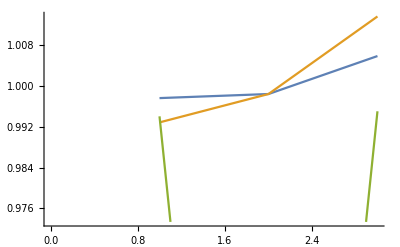

```mathematica
ListLinePlot[{{error[1][[1]],error[2][[1]],error[3][[1]]},
{error[1][[2]],error[2][[2]],error[3][[2]]},
{error[1][[3]],error[2][[3]], error[3][[3]]}}]
```

```mathematica
{error[1][[1]]}
```

{0.997606}

```mathematica
ListLinePlot[error[[1:3]][[1]]]
```

```mathematica
Prusa Calibration 12/3/2017
```

(4 Calibration Prusa)/2017

```mathematica
defaultstep={79.98,80.01,405.784};
newstep[0] = defaultstep;
ideal[1] = {25, 25, 20};
act[1] = {24.84, 24.90,20.71};
error[1]
newstep[1]
```

{1.00644,1.00402,0.965717}

{80.4952,80.3313,391.873}

```mathematica
ideal[2] = {25,25,25};
act[2] = {25.29, 25.11, 24.24};
error[2]
newstep[2]
```

{0.988533,0.995619,1.03135}

{79.5721,79.9794,404.159}

```mathematica
(Abs[newstep[1]+newstep[2]]/2)
Abs[error[1]+error[2]]/2
```

{80.0337,80.1554,398.016}

{0.997487,0.999818,0.998535}

## Prusa Calibration 11/24/2018

```mathematica
defaultstep={78.8939,80.99,404.90};
newstep[0] = defaultstep;
ideal[1] = {25, 25, 20};
act[1] = {25.14, 25.24,20.22};
error[1]
newstep[1]
```

{0.994431,0.990491,0.98912}

{78.4546,80.2199,400.495}